```mathematica
D[y^n/(k^n+y^n),{y,2}]//FullSimplify
```

(k^n n y^(-2+n) (k^n (-1+n)-(1+n) y^n))/((k^n+y^n)^3)

## Initialization

```mathematica
Clear["Global`*"]
```

Approximate value of fN

```mathematica
fN1[a0in_]:=Module[{a0=a0in, R,N=121, fa0, G, Acell, L}, 
R = 0.2*a0;
fa0 = Sinh[R]Exp[R-a0]/a0;
G = 2π Exp[R] Sinh[R];
Acell = Sqrt[3]/2 a0^2;
L = Sqrt[ (N-7)Acell/π + (a0/2)^2];
fNest = 6fa0+G/Acell(Exp[-1.5 a0]- Exp[-L]);
fNinf = 6fa0+G/Acell Exp[-1.5 a0]
];
fN1[1.5]
```

0.506583

```mathematica
params = {fN-> fNinf, n-> 2};
params2 = {Con -> 16,k-> 8, fN-> fNinf, n-> 2};
params3 = {Con -> 16,k-> 8, n-> 2};
```

Values for fN:
N=121, a0 = 0.5 => 
N=121, a0 = 1.5 =>

Updating function

```mathematica
f[p_]:=((1+fN)^n((Con-1)p+1)^n)/(k^n+(1+fN)^n((Con-1)p+1)^n);
Constart = 1;
kstart = 1;
Conmax = 30;
Kmax=40;
ds=0.1;
```

## Number of fixed points

### Analytical solutions

```mathematica
y[x_]:=(1+fN)((Con-1)x+1);
asol=Solve[{0== y[x]^n/(k^n+y[x]^n)-x} /. {n-> 1}, {x}]
```

{{x→(-2+Con-2 fN+Con fN-k-√(Con^2+2 Con^2 fN+Con^2 fN^2+4 k-2 Con k+4 fN k-2 Con fN k+k^2))/(2 (-1+Con-fN+Con fN))},{x→(-2+Con-2 fN+Con fN-k+√(Con^2+2 Con^2 fN+Con^2 fN^2+4 k-2 Con k+4 fN k-2 Con fN k+k^2))/(2 (-1+Con-fN+Con fN))}}

```mathematica
Δ = FullSimplify[Con^2+2 Con^2 fN+Con^2 fN^2+4 k-2 Con k+4 fN k-2 Con fN k+k^2] (*Δ*)
```

Con^2 (1+fN)^2-2 (-2+Con) (1+fN) k+k^2

```mathematica
a =(-1+Con-fN+Con fN)// FullSimplify (*a*)
b = FullSimplify[-2+Con-2 fN+Con fN-k] (*b*)
c =  (b^2-Δ)/(4 a) // FullSimplify
```

(-1+Con) (1+fN)

(-2+Con) (1+fN)-k

-1-fN

```mathematica
b^2 - 4 a c // Expand
Δ // Expand
```

Con^2+2 Con^2 fN+Con^2 fN^2+4 k-2 Con k+4 fN k-2 Con fN k+k^2

Con^2+2 Con^2 fN+Con^2 fN^2+4 k-2 Con k+4 fN k-2 Con fN k+k^2

```mathematica
Plot3D[(-2+Con-2 fN+Con fN-k+√(Con^2+2 Con^2 fN+Con^2 fN^2+4 k-2 Con k+4 fN k-2 Con fN k+k^2))/(2 (-1+Con-fN+Con fN))/.{fN->10}, {Con,1,30},{k,1,30}]
```

-Graphics3D-

Rewrite equation into
 -(C_on-1)^2 X^3+[(C_on-1)^2 -2 (C_on-1)]X^2 + [2(C_on-1) - 1 - K^2/((1 + f_N)^2)]X + 1 =0

Δ = 18 a b c d - 4 b^3 d + b^2 c^2 - 4 a c^3 - 27 a^2 d^2;
Δ > 0: three distinct roots

```mathematica
a=  -(Con-1)^2;
b = (Con-1)^2 -2 (Con-1);
c =  2(Con-1) - 1 - k^2/((1 + fN)^2);
d = 1;
Δ = 18 a b c d - 4 b^3 d + b^2 c^2 - 4 a c^3 - 27 a^2 d^2;
Apart[Δ]
```

-(4 (-1+Con)^2 Con^3 k^2)/(1+fN)^2+((-1+Con)^2 (-27+18 Con+Con^2) k^4)/(1+fN)^4-(4 (-1+Con)^2 k^6)/(1+fN)^6

```mathematica
ksol=Solve[-(4 (-1+Con)^2 Con^3 k2)/(1+fN)^2+((-1+Con)^2 (-27+18 Con+Con^2) k2^2)/(1+fN)^4-(4 (-1+Con)^2 k2^3)/(1+fN)^6==0, k2];
```

To match with plot below:
Con = 1+ 0.1*n, where n is the index that runs from 1 to 291.

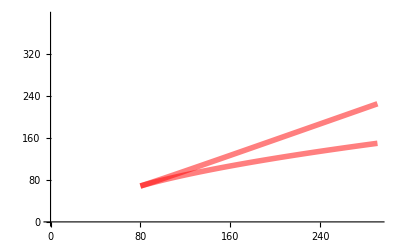

```mathematica
plot1 = Plot[ ((k2 /. ksol[[2;;]] )^(1/2)-kstart)/ds/. params /. {Con-> Constart+idx*ds}, {idx,1, (Conmax-Constart)/ds+1}, PlotStyle-> { Thickness[0.01], RGBColor[1,0,0, 0.5]}];
Show[plot1, AxesOrigin-> {0,0}, PlotRange-> {{0,(Conmax-1)/ds+1},{0, (Kmax-1)/ds+1}}]
```

### Plot 3 D phase diagram

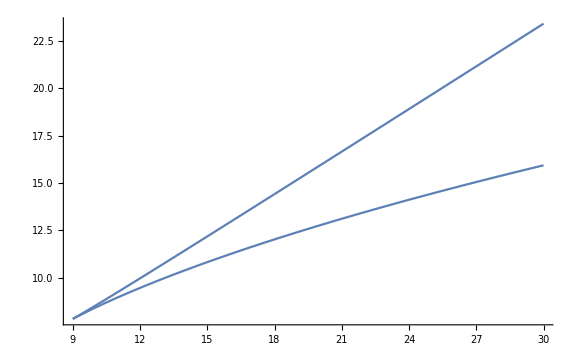

```mathematica
Plot[ Sqrt[(k2/.ksol[[2;;]])] /. {fN-> fN1[1.5]}, {Con,1,30},  PlotRange-> All,ImageSize->Large]
```

```mathematica
a0ticks0={{1,""},{1.5,""},{2.5,""},{3,""},{3.5,""},{4.5,""},{5,""},{5.5,""}};
a0ticks=Join[{0.5,2,4,6}, a0ticks0];
Plot3D[ Sqrt[(k2/.ksol[[2;;]]) /. {fN-> fN1[a0]}], {Con,1,30}, {a0, 0.5,6}, PlotRange-> All, BoxRatios->{1, 1, 1},ImageSize->Large, AxesLabel->{"C_ON","a_0","K"}, BaseStyle->{FontSize->20}, Mesh-> None, PlotStyle->Directive[Opacity[0.5]], Ticks-> {Automatic,a0ticks, Automatic}]
```

-Graphics3D-

### Stability condition

#### Approximate condition

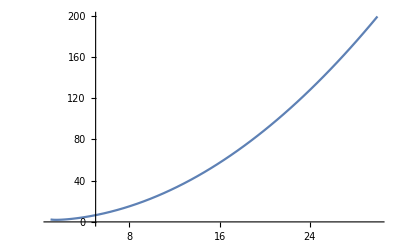

```mathematica
fcon = 1/2(k^2/(1+fN)^2+ (1+fN)^2/k^2)+1;
Plot[fcon /. params, {k,1,30}]
```

#### Using exact solution

Problem: xs is not necessarily the stable solution. It could even be imaginary.

```mathematica
Re[cond/.params /.{k-> 17,Con-> 20}  // Simplify]
```

1.03275

```mathematica
xs/.params /.{k-> 17,Con-> 20}
```

0.441598-0.212142 ⅈ

```mathematica
xs = x/.asol[[1]];
cond =(n*y[xs]^(n-1) k^n)/((k^n+y[xs]^n)^2)(Con-1)(1+fN);
data=Boole@Table[(Re[cond/.params // Simplify] )<1,{k, 1, 40,ds}, {Con, 2, Conmax, ds}];
```

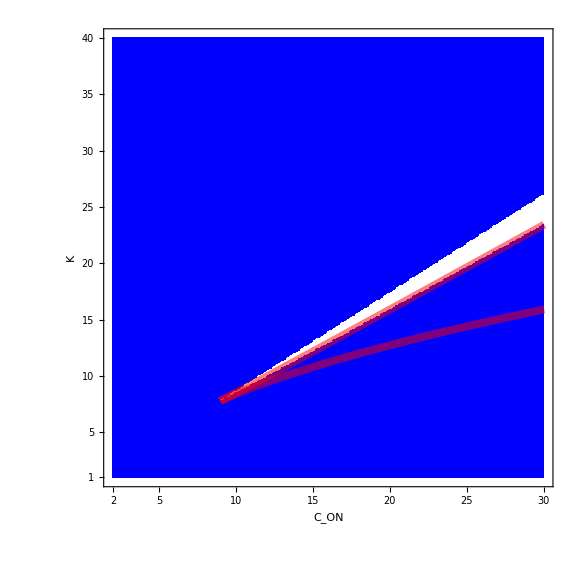

```mathematica
Conlist = Range[2,Conmax, ds];
tick1[n_]:= {(n-1)/(ds)+1,klist[[(n-1)/(ds)+1]]};
tick2[n_]:= {(n-1)/ds+1,Conlist[[(n-1)/ds+1]]};
vticks = { Rationalize/@Join[{tick1[1]}, tick1/@Range[5,Kmax,5]], None};
hticks ={ Rationalize/@Join[{tick2[1]}, tick2/@Range[5-1,Conmax-1,5]], None};
ticks = {vticks,hticks};
plot3=ArrayPlot[data,DataReversed -> True, ImageSize-> Large,BaseStyle->{FontSize-> 32},Frame-> True, FrameLabel-> {"K","C_ON"}, FrameTicks-> ticks, ColorRules->{1->Blue,3->LightYellow}, AspectRatio->1];
Show[plot3,plot1b]
```

#### B = 0 line

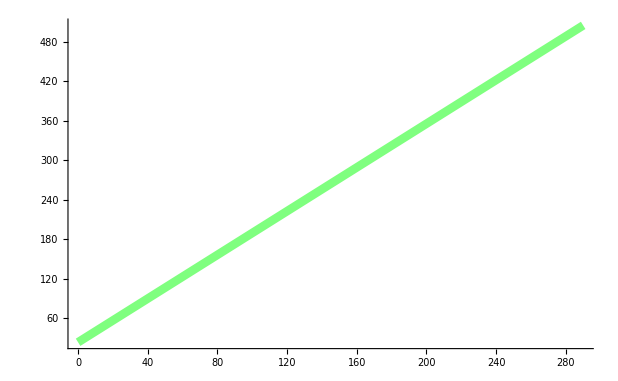

```mathematica
Kfunc = (Con+1)/2(1+fN);
plot4 = Plot[Kfunc /. params, {Con, Constart,Conmax}, PlotStyle-> {RGBColor[0,1,0, 0.5], Thickness[0.01]}, AxesOrigin-> {0,0}];
plot4b = Plot[(Kfunc-kstart)/ds/. params /. {Con-> Constart+idx*ds}, {idx,0, (Conmax-Constart)/ds}, PlotStyle-> {RGBColor[0,1,0, 0.5], Thickness[0.01]}, AxesOrigin-> {0,0}, PlotRange-> All]
```

### Numerical calculation

```mathematica
sol=NSolve[{(f[p] /. params2) == p,0≤p≤ 1}, p]
Plot[{f[p]/.params, p},{p,0,1}]
```

```mathematica
Manipulate[Plot[{((1+fN)^n((Con-1)p+1)^n)/(k^n+(1+fN)^n((Con-1)p+1)^n), p},{p,0,1}], {n,1,2},{Con,1,30},{k,1,20},{fN,0.1, 4}]
```

### Solve over range of K-Con

Values for fN: 
a0=0.5 -> fN = 2.2983
a0=1.5 -> fN = 0.5108

```mathematica
(*nsteps=100;*)
klist = Range[kstart,Kmax,ds];
Conlist = Range[Constart,Conmax, ds];
```

```mathematica
nsol = Table[
Length[NSolve[{(f[p] /. params/. {k-> klist[[j]], Con-> Conlist[[i]]} ) == p,0≤p≤ 1}, p]] ,
{i,1,Length[Conlist]},{j,1,Length[klist]}];
```

Automatically calculate ticks

```mathematica
tick1[n_]:= {(n-kstart)/(ds)+1,klist[[(n-kstart)/(ds)+1]]};
tick2[n_]:= {(n-Constart)/ds+1,Conlist[[(n-Constart)/ds+1]]};
kticks = { Rationalize/@Join[{tick1[kstart]}, tick1/@Range[5,Kmax,5]], None};
Conticks ={ Rationalize/@Join[{tick2[Constart]}, tick2/@Range[5,Conmax,5]], None};
```

Manually set ticks

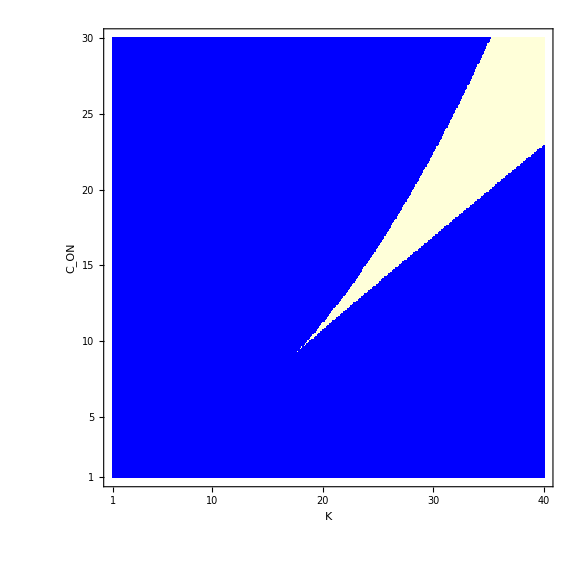

```mathematica
ticks={Conticks, kticks};
plot2=ArrayPlot[nsol, DataReversed -> True, ImageSize-> Large,BaseStyle->{FontSize-> 32},Frame-> True, FrameLabel-> {"C_ON","K"}, FrameTicks-> ticks, ColorRules->{1->Blue,3->LightYellow}, AspectRatio->1]
```

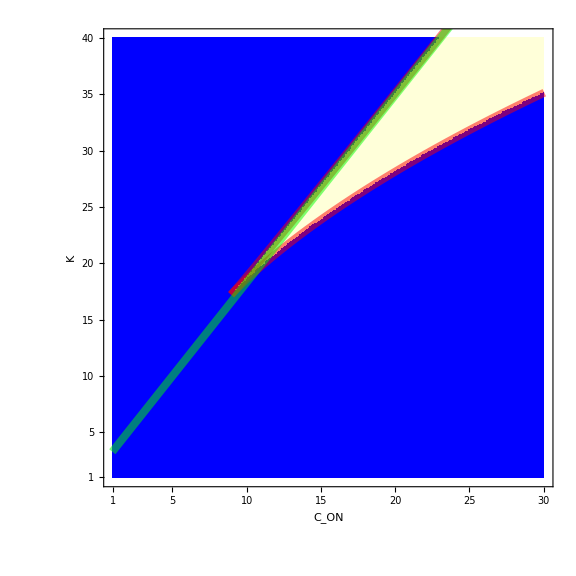

```mathematica
ticks={kticks, Conticks};
range= {{0,(Conmax-Constart)/ds+1},{0, (Kmax-kstart)/ds+1}};
plot2=ArrayPlot[Transpose[nsol], DataReversed -> True, ImageSize-> Large,BaseStyle->{FontSize-> 32},Frame-> True, FrameLabel-> {"K","C_ON"}, FrameTicks-> ticks, ColorRules->{1->Blue,3->LightYellow}, AspectRatio->1];
Show[plot2, plot1,plot4b, PlotRange-> range]
```

### Solve over range of B

Scaling of p (magnetization) against B shows behaviour similar to spin systems. When bistable points are possible, bifurcation implies more complicated scaling.

{{p→1/2},{p→(5-6 Con+Con^2-(-1+Con) √(-7-10 Con+Con^2))/(2 (2-4 Con+2 Con^2))},{p→(5-6 Con+Con^2+(-1+Con) √(-7-10 Con+Con^2))/(2 (2-4 Con+2 Con^2))}}

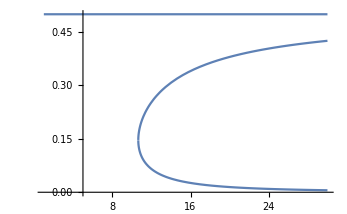

```mathematica
sol=Solve[{f[p] ==p} /. {n-> 2,k-> (Con+1)/2*(1+fN)}, {p}]
Plot[p /. sol, {Con, 1,30}]
```

```mathematica
Bvals = Range[-5, 5, 0.1];
Convals = ConstantArray[5,Length[Bvals]];
Kvals = (Convals+1)/2*(1+fN)-Bvals /. {fN-> fNinf};
Convals2 = ConstantArray[8,Length[Bvals]];
Kvals2 = (Convals2+1)/2*(1+fN)-Bvals /. {fN-> fNinf};
```

```mathematica
nsol = Table[
NSolve[{(f[p] /. params/. {k-> Kvals[[i]], Con-> Convals[[i]]} ) == p,0≤p≤ 1}, p] ,
{i,1,Length[Bvals]}];
nsol2 = Table[
NSolve[{(f[p] /. params/. {k-> Kvals2[[i]], Con-> Convals2[[i]]} ) == p,0≤p≤ 1}, p] ,
{i,1,Length[Bvals]}];
```

```mathematica
Bvals2a=Table[ ConstantArray[Bvals[[i]], (Length/@nsol2)[[i]] ], {i,1,Length[Bvals]}];
data2=Flatten[Transpose[{Bvals2a,2*(p/.nsol2)-1}],{3}];
```

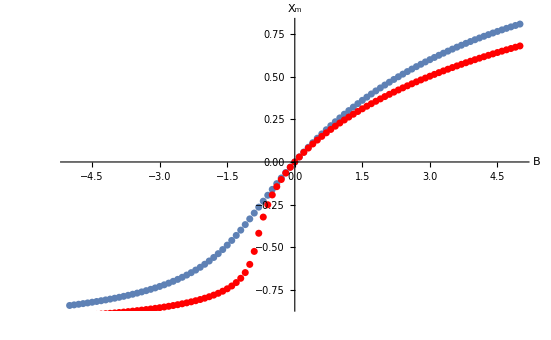

```mathematica
pvals = First/@(p/.nsol);
pvals2 = First/@(p/.nsol2);
p1=ListPlot[Transpose[{Bvals,2*pvals-1}]];
p2=ListPlot[data2, PlotStyle-> {Red}];
Show[p1,p2, AxesLabel-> {"B","X_m"}]
```

### Solve over range of a0

Apparently not all solutions are found in the method below:

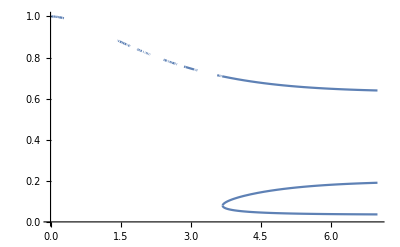

```mathematica
sol=Solve[{f[p] ==p} /. params3 , {p}];
Plot[p /. sol /. {fN-> fN1[a0]}, {a0, 0, 7}]
```

Instead, if we solve for pre-defined a0 values, it seems to work

```mathematica
a0vals = Range[0.5,7, 0.01];
nsol = Table[
NSolve[{(f[p] /. params3 /. {a0-> a0vals[[i]], fN-> fN1[a0vals[[i]]]}) == p,0≤p≤ 1}, p] ,
{i,1,Length[a0vals]}];
a0vals2=Table[ ConstantArray[a0vals[[i]], (Length/@nsol)[[i]] ], {i,1,Length[a0vals]}];
data2=Flatten[Transpose[{a0vals2,p/.nsol}],{3}];
```

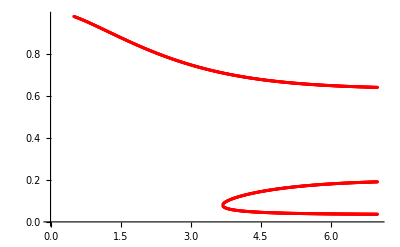

```mathematica
p2=ListPlot[data2, PlotStyle-> {Red}]
```

## Bifucation diagram

Make a bifurcation diagram across bistable region

```mathematica
npoints = 2000; 
Conlist = Range[1,30,29/npoints];
Klist = Range[1,30,29/npoints];
sol = ConstantArray[0,1000];
f[p_]:=((1+fN)^n((Con-1)p+1)^n)/(k^n+(1+fN)^n((Con-1)p+1)^n);
sol = Table[
p/. NSolve[{(f[p] /. {k-> Klist[[i]], Con-> 20, fN-> 0.5108, n->2} ) == p,0≤p≤ 1}, p] ,
{i,1,npoints}];
```

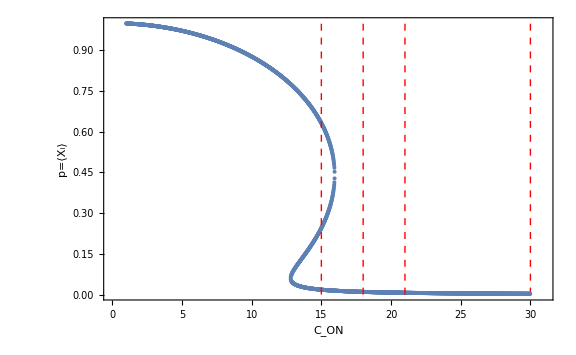

```mathematica
linestyle={Red, Thick, Dashed};
line1 = Line[{{15, 0},{15,1}}];
line2 = Line[{{18, 0},{18,1}}];
line3 = Line[{{21, 0},{21,1}}];
line4 = Line[{{30, 0},{30,1}}];
nsol=Flatten[Dimensions/@sol];
nsol2=Table[ConstantArray[Conlist[[i]], nsol[[i]] ],{i,1,npoints}];
data=Transpose[{Flatten[nsol2],Flatten[sol]}];
plot=ListPlot[data,BaseStyle->{FontSize-> 24},ImageSize-> Large, Frame-> True, FrameLabel-> {"C_ON","p=⟨X_i⟩"}, PlotStyle-> {PointSize[0.005]},PlotRange-> {{0,31},{0,1}}, Epilog->{Directive[linestyle],line1,line2,line3,line4}]
```

```mathematica
fnamestr = StringReplace["bifurcation_Kval1_Conval2toval3_a0_val4_nval5_vert_lines.pdf",{"val1"-> "14", "val2"->"1","val3"-> "30", "val4"-> "1p5", "val5"->"2"}];
fname=FileNameJoin[{NotebookDirectory[], "fixed_points_uniform_lattice",fnamestr}];

(*Export[fname,plot ]*)
```

## Input-output bounds

Equivalent to dynamics of uniform lattice starting with X_m=0 or X_m=1. Non-uniform states can be outside these bounds, so not really informative.

```mathematica
RSolve[{x0[m] == 1/(1+k^n*((1+fN) x0[m-1])^(-n)), x0[0]== 1} /. {n->2},{x0}, m]
```

RSolve[{x0[m]==1/(1+k^2/((1+fN)^2 x0[-1+m]^2)),x0[0]==1},{x0},m]

```mathematica
recsol =Map[FullSimplify,RecurrenceTable[{x0[m] == 1/(1+k^n*((1+fN) x0[m-1])^(-n)), x0[0]== 1},{x0}, {m,0,10} ], 2]
```

$Aborted

## Critical a0 to turn OFF cell ON

Calculate critical a0 (or fN) required to turn an OFF cell ON if all the other cells are ON:
(1) Solve single cell system 
(2) Use solution to calculate secretion rate of single ON cell, single OFF cell and transition point (Unstable state).

NB Only for when bistability of single cell and uniform lattice coincide. Otherwise different types of behaviour are possible.

```mathematica
params3 = {Con -> 16,k-> 8, n-> 2};
xsol=NSolve[((Con-1)x+1)^n/(k^n+((Con-1)x+1)^n)==x /. params3, x];
xs=Sort[x /. xsol];
S[x_]:= (Con-1)*x + 1;
```

### Full lattice

```mathematica
fNc = S[Last@xs]^(-1) (k (xs[[2]]/(1-xs[[2]]))^(1/n) - S[ First@xs]) /. params3
```

0.236068

{a0→2.27234}

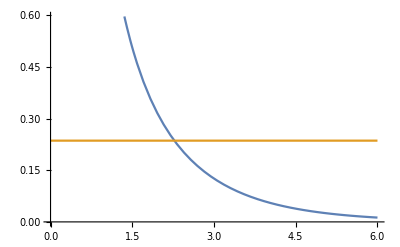

```mathematica
Ntot = 121;
R = 0.2*a0;
fa0 = Sinh[R]Exp[R-a0]/a0;
G = 2π Exp[R] Sinh[R];
Acell = Sqrt[3]/2 a0^2;
L = Sqrt[ (Ntot-7)Acell/π + (a0/2)^2];
L=∞;
fNest = 6fa0+G/Acell(Exp[-1.5 a0]- Exp[-L]);
sol=FindRoot[fNc -fNest, {a0, 5}]
Plot[{fNest, fNc}, {a0,0,6}]
```

### Nearest neighbour approximation

```mathematica
a0c[pin_,non_]:=Module[{R,Ntot=121, fa0, G, Acell, L, p=pin}, 
R = 0.2*a0;
fa0 = Sinh[R]Exp[R-a0]/a0;
G = 2π Exp[R] Sinh[R];
Acell = Sqrt[3]/2 a0^2;
L = Sqrt[ (Ntot-7)Acell/π + (a0/2)^2];
xm = (p-6/Ntot)/(1-p);
LHS = S[First@xs] + non fa0 S[Last@xs] + (6-non) fa0 S[First@xs] + (G/Acell(Exp[-1.5 a0]- Exp[-L]))*S[xm];
RHS =  k (xs[[2]]/(1-xs[[2]]))^(1/n);
sol=FindRoot[LHS -RHS /. params3, {a0, 5}];
Plot[{LHS/. params3,RHS/. params3}, {a0,0,6}];
a0/.sol
];
a0c[0.5, 4]
```

2.07111

```mathematica
dx=0.02;
a0cvals=Table[a0c[pin, non], {non,0,6},{pin,0,0.98,dx}];
plotdata=Map[Transpose[{Range[0,0.98,dx],#}]& , a0cvals];
p1=ListPlot[plotdata];
p1b=ListPlot[plotdata, Joined-> True, PlotLegends-> Range[6]];
```

OptionValue::nodef: Unknown option "PlotLegends" for Graphics.

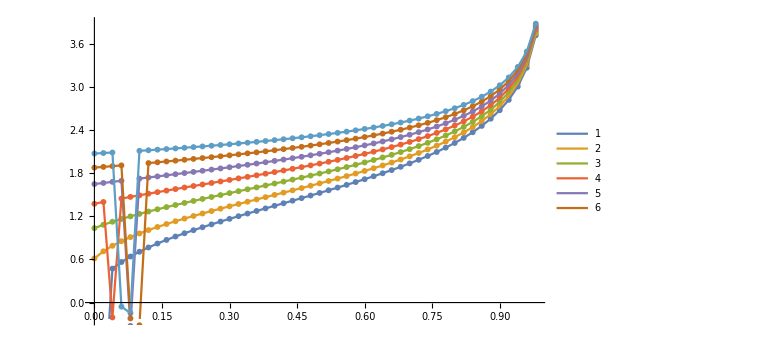

```mathematica
Show[p1, p1b, PlotLegends-> {"1","2"},ImageSize-> Large]
```